```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Read Results

```mathematica
InterpolateData[data_]:=Module[{temp},
temp = data;
(*Do[temp⟦ii⟧={{temp⟦ii,1⟧,temp⟦ii,2⟧},temp⟦ii,3⟧},{ii,1,Length[data]}];*)
Do[temp⟦ii⟧={temp⟦ii,1⟧,temp⟦ii,2⟧},{ii,1,Length[data]}];
Interpolation[temp,InterpolationOrder->1]
]
```

```mathematica
Clear[jOmega]
```

```mathematica
(*uExact[x_,y_]:=Sin[π x]Sin[π y];*)
uExact[x_]:=Sin[π x];
(*AdjExact[x_,y_]:=Sin[π x]Sin[π y];*)
AdjExact[x_,y_]:=Exp[-(x-0.5)^2*100-(y-0.5)^2*100];
(*jOmega[x_,y_]:=-π(Cos[π x]Sin[π y]+Cos[π y]Sin[π x]);*)
(*jOmega[x_,y_]:=200  ⅇ^(-100 (0.5-1 x+x^2- y+y^2)) (-1+x+y);*)
jOmega[x_]:=-π Cos[π x];
cycles = 15;
```

```mathematica
Clear[resultPrimalInt,temp,errorVariation]
```

```mathematica
Do[resultPrimal[ii] =Import[StringJoin["../2D_advection_gaussian/result_cycle",ToString[ii],".txt"],"Table"];

,{ii,0,cycles-1}];

Do[resultAdj[ii] =Import[StringJoin["../2D_advection_gaussian/resultAdj_cycle",ToString[ii],".txt"],"Table"];errorPred[ii] =Import[StringJoin["../2D_advection_gaussian/error_predicted_cycle",ToString[ii],".txt"],"Table"];
errorObs[ii] =Import[StringJoin["../2D_advection_gaussian/error_observed_cycle",ToString[ii],".txt"],"Table"];
(*errorVariation[ii]=Transpose[{resultPrimal[ii]⟦All,1⟧,1/(2^(ii+1)10)jOmega[resultPrimal[ii]⟦All,1⟧]*(uExact[resultPrimal[ii]⟦All,1⟧]-resultPrimal[ii]⟦All,2⟧)}];*)
,{ii,0,cycles-2}];
```

## Compute Error

```mathematica
ComputeError[adjoint_,primal_]:=Module[{faces,error,intAdj,anRight,anLeft},
intAdj = Interpolation[adjoint];
faces = Range[0,1,primal⟦2,1⟧-primal⟦1,1⟧];
error = Table[0,{ii,1,Length[primal]}];

(*Loop over the interior cells*)
Do[anRight = 1;
anLeft = -1;
error⟦ii⟧=1/2 intAdj[faces⟦ii⟧](anLeft-1)*(primal⟦ii,2⟧-primal⟦ii-1,2⟧),{ii,2,Length[error]-1}];

error

]
```

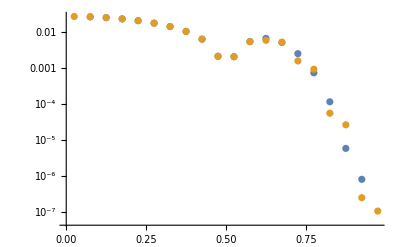

```mathematica
ListLogPlot[{Transpose[{errorPred[0]⟦All,1⟧,Abs[ComputeError[resultAdj[0],resultPrimal[0]]]}],Transpose[{errorPred[0]⟦All,1⟧,Abs[errorPred[0]⟦All,2⟧]}]}]
```

```mathematica
plotcycle=1;
ListPlot[{Transpose[{errorPred[plotcycle]⟦All,1⟧,errorPred[plotcycle]⟦All,2⟧}],Transpose[{errorObs[plotcycle]⟦All,1⟧,errorObs[plotcycle]⟦All,2⟧}]},PlotMarkers->{"*","o","<"}]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{errorObs[0]⟦All,1⟧,errorObs[0]⟦All,2⟧}],Transpose[{errorObs[5]⟦All,1⟧,errorObs[5]⟦All,2⟧}]},PlotMarkers->{"*","o","<"},PlotRange->Full]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{errorPred[0]⟦All,1⟧,errorPred[0]⟦All,2⟧}],Transpose[{errorPred[3]⟦All,1⟧,errorPred[3]⟦All,2⟧}]},PlotMarkers->{"*","o","<"},PlotRange->Full]
```

-Graphics-

```mathematica
Total[errorPred[0]⟦All,2⟧]
```

-0.634979

```mathematica
Total[errorPred[1]⟦All,2⟧]
```

-0.615414

```mathematica
Total[errorPred[2]⟦All,2⟧]
```

-0.608254

```mathematica
Total[errorPred[3]⟦All,2⟧]
```

-0.603729